## Wobbling Frequencies - New Boson

```mathematica
ClearAll["Global`*"]
```

```mathematica
inertiaFactor[moi_]:=1/(2*moi);
moi1Const=91;
moi2Const=9;
moi3Const=51;
A1Const=inertiaFactor[moi1Const];
A2Const=inertiaFactor[moi2Const];
A3Const=inertiaFactor[moi3Const];
jConst=13/2;
IConst=55/2;
```

```mathematica
jVec[jAbs_,theta_]:={jAbs*Cos[theta],jAbs*Sin[theta],0};
```

```mathematica
omega[I_,j_,theta_,A1_,A2_,A3_]:=(((2I+1)(A2-A1-(A2*jVec[j,theta][[2]])/I)+2A1*jVec[j,theta][[1]])*((2I+1)(A3-A1)+2A1*jVec[j,theta][[1]])-(A3-A1)*(A2-A1-(A2*jVec[j,theta][[2]])/I))^(1/2);
omegaP[I_,j_,theta_,A1_,A2_,A3_]:=(((2I+1)(A2-A1-(A2*jVec[j,theta][[2]])/I)-2A1*jVec[j,theta][[1]])*((2I+1)(A3-A1)-2A1*jVec[j,theta][[1]])-(A3-A1)(A2-A1-(A2*jVec[j,theta][[2]])/I))^(1/2);
```

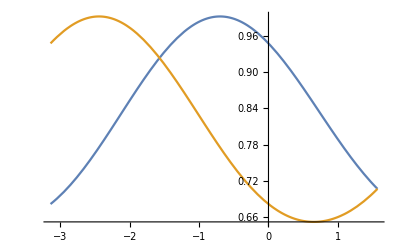

```mathematica
Plot[{omega[IConst,jConst,x,A1Const,A2Const,A3Const],omegaP[IConst,jConst,x,A1Const,A2Const,A3Const]},{x,-π,π/2}]
```